```mathematica
SetDirectory[NotebookDirectory[]]
```

F:\Dropbox\UNI\Projekte\A03_Hydraulics_Implementation\Avitabile

```mathematica
data =Import["Avitabile_AGB_Ref_data.xlsx"]
```

{{{x,y,CODE,AGB},{-99.9128,23.3776,CAM1,16.3333},{-106.438,23.3692,CAM1,10.9884},{-110.079,23.3609,CAM1,23.3889},{-106.229,23.3276,CAM1,15.2222},{-104.429,23.3192,CAM1,26.956},{-104.196,23.2942,CAM1,21.4167},14465,{150.071,-27.9891,AUS1,3.56173},{150.254,-27.9891,AUS1,4.44136},{150.287,-27.9891,AUS1,7.64506},{150.371,-27.9891,AUS1,7.14815},{150.379,-27.9891,AUS1,58.3642},{150.396,-27.9891,AUS1,74.892},{150.429,-27.9891,AUS1,14.2809}},{1}}
 |  |  |  |

```mathematica
lons =Rest@data[[1,All,1]];
lats =Rest@data[[1,All,2]];

agb = Rest@data[[1,All,4]];
```

```mathematica
ssc =Transpose[{lons,lats}]
```

{{-99.9128,23.3776},{-106.438,23.3692},{-110.079,23.3609},{-106.229,23.3276},{-104.429,23.3192},{-104.196,23.2942},{-109.838,23.2442},{-103.063,23.2192},{-99.1545,23.2026},{82.3288,23.1942},{-106.146,23.1609},{-99.8295,23.1609},14455,{149.829,-27.9891},{149.904,-27.9891},{149.937,-27.9891},{150.054,-27.9891},{150.071,-27.9891},{150.254,-27.9891},{150.287,-27.9891},{150.371,-27.9891},{150.379,-27.9891},{150.396,-27.9891},{150.429,-27.9891}}
 |  |  |  |

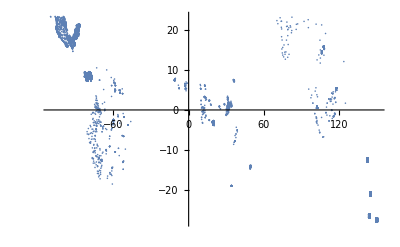

```mathematica
ListPlot[ssc]
```

```mathematica
rounded=Round[(ssc+0.25)*2]/2 -0.25
```

{{-99.75,23.25},{-106.25,23.25},{-110.25,23.25},{-106.25,23.25},{-104.25,23.25},{-104.25,23.25},{-109.75,23.25},{-103.25,23.25},{-99.25,23.25},{82.25,23.25},{-106.25,23.25},{-99.75,23.25},{-99.25,23.25},{-103.25,23.25},{-103.75,23.25},{-99.25,23.25},{-101.25,23.25},{-100.75,23.25},{-104.25,23.25},{-104.25,23.25},{-104.25,23.25},{-102.75,23.25},14434,{149.75,-27.75},{149.75,-27.75},{149.75,-27.75},{149.75,-27.75},{150.25,-27.75},{150.25,-27.75},{150.25,-27.75},{150.25,-27.75},{149.75,-27.75},{149.75,-27.75},{149.75,-27.75},{149.75,-27.75},{149.75,-27.75},{149.75,-27.75},{150.25,-27.75},{150.25,-27.75},{150.25,-27.75},{150.25,-27.75},{150.25,-27.75},{150.25,-27.75},{150.25,-27.75},{150.25,-27.75}}
 |  |  |  |

```mathematica
uniqueCoords =DeleteDuplicates[rounded];
```

```mathematica
positions = Table[Flatten[Position[rounded,uniqueCoords[[i]]],1],{i,1,Length@uniqueCoords}]
```

{1}
 |  |  |  |

```mathematica
agbhalb = Table[agb[[positions[[i]]]],{i, 1, Length@positions}]
```

{{16.3333,5.625},828,{5.42284,3.16358,9.02778,14.4352,5.46296,4.18827,24.358,5.29012,15.1173,29.6204,48.6296,13.8086,31.5648,63.2099,2.30247,26.4691,9.49691,1.21296,1.17901,1.14198,41.0432,21.9568,10.1914,6.71914,16.6481,256,10.284,7.91667,24.4012,115.466,20.5247,14.7284,7.19136,1.10185,21.2006,85.5679,63.75,28.3611,22.9877,14.4167,12.6821,85.75,75.6605,9.03704,3.56173,4.44136,7.64506,7.14815,58.3642,74.892,14.2809}}
 |  |  |  |

```mathematica
meanAGBhalb =Table[Mean[agbhalb[[i]]] /10.0,{i,1,Length@positions}];
```

```mathematica
agbhalb[[4]]
```

{26.956,21.4167,21.5394,18.8125,27.2847}

```mathematica
meanAGBhalb[[4]]
```

2.32019

```mathematica
Table[StandardDeviation[agbhalb[[i]]] /10.0,{i,1,Length@positions}];
```

StandardDeviation::shlen: The argument {23.3889} should have at least two elements.

StandardDeviation::shlen: The argument {27.7708} should have at least two elements.

StandardDeviation::shlen: The argument {11.1854} should have at least two elements.

General::stop: Further output of StandardDeviation :: shlen will be suppressed during this calculation.

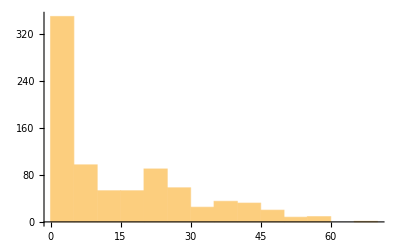

```mathematica
Histogram[meanAGBhalb]
```

```mathematica
Table[

If[Length[agbhalb[[i]]]>1,
StandardDeviation[agbhalb[[i]]] /10.0],{i,1,Length@positions}];
```

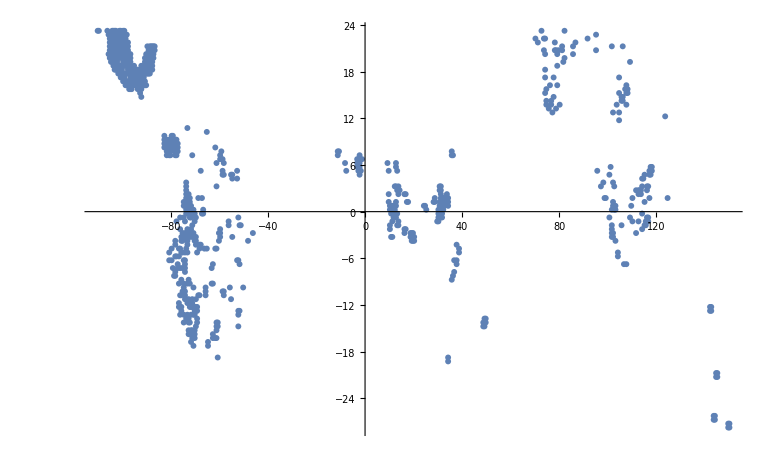

```mathematica
ListPlot[uniqueCoords]
```

```mathematica
basinCoords = Import["F:\\ClimateData\\Amazon\\Amazon_basin_coords.txt","Table","FieldSeparators"->"\t"]
```

{{-64.25,-20.25},{-63.75,-20.25},{-63.25,-20.25},{-64.25,-19.75},{-63.75,-19.75},{-63.25,-19.75},{-62.75,-19.75},{-62.25,-19.75},{-64.25,-19.25},{-63.75,-19.25},{-63.25,-19.25},{-62.75,-19.25},{-62.25,-19.25},{-66.25,-18.75},{-65.75,-18.75},{-65.25,-18.75},{-64.75,-18.75},{-64.25,-18.75},{-63.75,-18.75},{-63.25,-18.75},{-62.75,-18.75},{-62.25,-18.75},{-61.75,-18.75},1900,{-62.25,3.25},{-61.75,3.25},{-61.25,3.25},{-60.75,3.25},{-60.25,3.25},{-59.75,3.25},{-64.25,3.75},{-63.75,3.75},{-63.25,3.75},{-62.25,3.75},{-61.75,3.75},{-61.25,3.75},{-60.75,3.75},{-60.25,3.75},{-59.75,3.75},{-61.75,4.25},{-61.25,4.25},{-60.75,4.25},{-60.25,4.25},{-59.75,4.25},{-60.75,4.75},{-60.25,4.75},{-59.75,4.75}}
 |  |  |  |

```mathematica
posInAB = Flatten[Table[Position[ basinCoords,uniqueCoords[[i]]],{i, 1, Length@uniqueCoords}],2]
```

{1926,1884,1860,1850,1851,1853,1857,1807,1803,1808,1755,1753,1759,1756,1754,1757,1758,1703,1700,1704,1701,1706,1714,1659,1650,1651,1658,1646,1645,1648,1652,1593,1598,1585,1594,1588,1633,1526,1533,1541,1569,1515,1485,1421,1454,1430,1427,1399,1369,1378,1376,1400,1371,1374,1322,1324,1315,1312,1313,1318,1354,1344,1316,1320,1317,1288,1268,1262,1257,1258,1252,1269,1213,1217,1206,1196,1216,1173,1148,1163,1159,1142,1143,1165,1172,1088,1087,1092,1100,1090,1026,1025,1028,977,1020,976,1021,920,943,965,914,886,862,860,858,864,809,703,697,651,670,669,646,642,649,632,594,602,612,561,544,542,575,576,490,506,526,491,494,505,511,448,446,483,451,454,445,397,398,401,352,351,356,350,354,355,309,307,308,343,254,257,296,259,251,260,207,216,209,170,169,174,191,190,158,157,133,117,109,91,93,94,72,56,25}

```mathematica
avitabileBasincoords = basinCoords[[posInAB]]
```

{{-61.25,3.25},{-72.75,2.25},{-67.25,1.75},{-73.75,1.75},{-73.25,1.75},{-72.25,1.75},{-68.75,1.75},{-72.75,1.25},{-74.75,1.25},{-72.25,1.25},{-73.75,0.75},{-74.75,0.75},{-71.75,0.75},{-73.25,0.75},{-74.25,0.75},{-72.75,0.75},{-72.25,0.75},{-72.25,0.25},{-73.75,0.25},{-71.75,0.25},{-73.25,0.25},{-70.75,0.25},{-66.75,0.25},{-66.75,-0.25},{-71.25,-0.25},{-70.75,-0.25},{-67.25,-0.25},{-73.25,-0.25},{-73.75,-0.25},{-72.25,-0.25},{-70.25,-0.25},{-72.25,-0.75},{-69.75,-0.75},{-76.25,-0.75},{-71.75,-0.75},{-74.75,-0.75},{-52.25,-0.75},{-77.75,-1.25},{-74.25,-1.25},{-70.25,-1.25},{-56.25,-1.25},{-56.25,-1.75},{-71.25,-1.75},{-76.25,-2.25},{-59.75,-2.25},{-71.75,-2.25},{-73.25,-2.25},{-60.25,-2.75},{-75.25,-2.75},{-70.75,-2.75},{-71.75,-2.75},{-59.75,-2.75},{-74.25,-2.75},{-72.75,-2.75},{-70.75,-3.25},{-69.75,-3.25},{-74.25,-3.25},{-75.75,-3.25},{-75.25,-3.25},{-72.75,-3.25},{-54.75,-3.25},{-59.75,-3.25},{-73.75,-3.25},{-71.75,-3.25},{-73.25,-3.25},{-60.25,-3.75},{-70.25,-3.75},{-73.25,-3.75},{-75.75,-3.75},{-75.25,-3.75},{-78.25,-3.75},{-69.75,-3.75},{-69.75,-4.25},{-67.75,-4.25},{-73.25,-4.25},{-78.25,-4.25},{-68.25,-4.25},{-61.25,-4.75},{-73.75,-4.75},{-66.25,-4.75},{-68.25,-4.75},{-76.75,-4.75},{-76.25,-4.75},{-65.25,-4.75},{-61.75,-4.75},{-75.25,-5.25},{-75.75,-5.25},{-73.25,-5.25},{-69.25,-5.25},{-74.25,-5.25},{-77.75,-5.75},{-78.25,-5.75},{-76.75,-5.75},{-74.25,-6.25},{-52.75,-6.25},{-74.75,-6.25},{-52.25,-6.25},{-74.25,-6.75},{-62.75,-6.75},{-51.75,-6.75},{-77.25,-6.75},{-63.25,-7.25},{-75.25,-7.25},{-76.25,-7.25},{-77.25,-7.25},{-74.25,-7.25},{-74.25,-7.75},{-72.75,-8.75},{-75.75,-8.75},{-72.25,-9.25},{-62.75,-9.25},{-63.25,-9.25},{-74.75,-9.25},{-76.75,-9.25},{-73.25,-9.25},{-55.75,-9.75},{-74.75,-9.75},{-70.75,-9.75},{-65.75,-9.75},{-65.75,-10.25},{-74.25,-10.25},{-75.25,-10.25},{-58.75,-10.25},{-58.25,-10.25},{-76.25,-10.75},{-68.25,-10.75},{-58.25,-10.75},{-75.75,-10.75},{-74.25,-10.75},{-68.75,-10.75},{-65.75,-10.75},{-72.75,-11.25},{-73.75,-11.25},{-55.25,-11.25},{-71.25,-11.25},{-69.75,-11.25},{-74.25,-11.25},{-73.25,-11.75},{-72.75,-11.75},{-71.25,-11.75},{-71.25,-12.25},{-71.75,-12.25},{-69.25,-12.25},{-72.25,-12.25},{-70.25,-12.25},{-69.75,-12.25},{-69.25,-12.75},{-70.25,-12.75},{-69.75,-12.75},{-52.25,-12.75},{-73.25,-13.25},{-71.75,-13.25},{-52.25,-13.25},{-70.75,-13.25},{-74.75,-13.25},{-70.25,-13.25},{-73.75,-13.75},{-69.25,-13.75},{-72.75,-13.75},{-72.25,-14.25},{-72.75,-14.25},{-69.25,-14.25},{-60.75,-14.25},{-61.25,-14.25},{-60.75,-14.75},{-61.25,-14.75},{-61.25,-15.25},{-71.75,-15.25},{-62.75,-15.75},{-62.75,-16.25},{-61.75,-16.25},{-61.25,-16.25},{-64.75,-16.75},{-64.75,-17.25},{-60.75,-18.75}}

```mathematica
basinAvitabileOverlapIndexces =Flatten[Table[Position[uniqueCoords,avitabileBasincoords[[u]]],{u, 1,Length@avitabileBasincoords}]]
```

{438,466,472,476,477,483,486,488,496,501,506,510,511,518,522,525,526,540,541,544,545,546,548,552,554,555,557,559,561,563,564,568,570,571,572,576,579,585,586,588,590,598,601,608,609,611,614,616,619,621,622,626,627,629,634,635,636,638,639,640,642,644,646,647,648,652,653,655,657,658,659,660,661,662,663,664,665,667,669,670,671,672,673,674,676,679,680,682,683,684,686,687,688,692,694,695,696,697,698,699,700,705,706,707,708,709,711,716,718,719,720,721,722,723,724,725,726,727,729,730,731,732,733,734,735,736,737,738,739,740,741,742,743,744,745,746,747,748,749,750,754,757,759,760,761,762,765,766,767,770,771,772,773,774,775,776,778,779,782,786,787,788,789,791,795,796,800,802,803,807,808,810,812,814,816}

```mathematica
Length@avitabileBasincoords
```

175

```mathematica
avitabileBasincoords//Length
```

175

```mathematica
meanBiomass =meanAGBhalb[[basinAvitabileOverlapIndexces]]
```

{32.6868,6.02366,36.3851,18.696,19.3184,22.419,34.8555,23.2652,6.99588,23.5134,22.4177,16.43,19.4856,22.8961,12.6492,21.3169,24.5293,25.2387,23.6638,23.6291,23.5777,23.0388,36.6626,37.7724,23.5768,24.6489,43.7609,23.5211,21.4712,24.9717,27.2505,22.1295,23.4709,23.2223,25.9722,26.7597,42.29,23.158,27.5264,26.4223,42.6536,33.918,26.3452,25.85,31.2174,26.5437,24.4825,29.822,24.1761,24.3581,23.6593,34.8757,25.8014,27.3972,25.2138,27.9269,24.8416,24.4367,24.9686,26.6897,35.8284,17.8947,25.5895,23.742,24.9281,24.6031,25.5825,24.4558,19.3208,22.7333,13.3131,23.2646,15.5318,37.4009,18.1649,23.8681,21.0372,23.8417,21.0838,27.7379,32.4983,19.3277,14.4519,31.9959,27.9738,17.2396,13.2735,27.5744,30.3498,4.77807,12.1914,0.367709,21.7127,13.0459,15.9564,24.4602,16.0628,18.3272,23.7088,14.4019,11.4809,23.9376,7.43915,15.3801,10.4039,22.9457,22.7237,18.3824,23.9249,21.6974,25.4659,30.8302,25.7766,0.166114,22.8304,20.9541,20.8019,18.9008,21.0577,24.0744,19.1823,21.6396,21.2695,18.4072,0.162124,14.7519,22.0783,0.0929667,14.2557,20.6708,26.6372,19.2986,7.07037,20.367,22.464,21.2401,5.0872,21.2681,24.562,27.3523,26.4671,18.2256,27.5395,8.76616,19.2226,24.7958,24.6719,24.5258,16.4766,15.1222,4.81428,13.9745,14.9943,18.2421,0.681818,18.6609,0.464888,10.1579,0.00711562,0.00445709,0.113188,0.0792361,21.6243,12.7055,25.0244,35.1047,15.8401,0.0192508,15.4559,14.1868,22.4822,20.8779,21.5005,19.308,15.6993}

```mathematica
basinCoords[[posInAB[[1]]]]
```

{-61.25,3.25}

```mathematica
uniqueCoords[[basinAvitabileOverlapIndexces[[1]]]]
```

{-61.25,3.25}

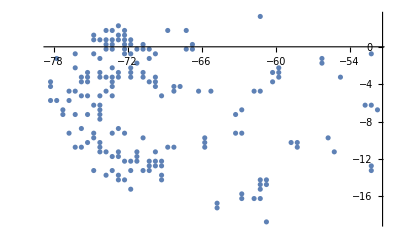

```mathematica
ListPlot[avitabileBasincoords]
```

```mathematica
dataXYZ = Transpose[{avitabileBasincoords[[All,1]],avitabileBasincoords[[All,2]],meanBiomass*0.5, posInAB}];
```

```mathematica
meanBiomass*0.5
```

{16.3434,3.01183,18.1925,9.34799,9.65921,11.2095,17.4278,11.6326,3.49794,11.7567,11.2088,8.21502,9.7428,11.448,6.32459,10.6584,12.2647,12.6193,11.8319,11.8146,11.7888,11.5194,18.3313,18.8862,11.7884,12.3245,21.8804,11.7605,10.7356,12.4859,13.6253,11.0648,11.7355,11.6111,12.9861,13.3799,21.145,11.579,13.7632,13.2112,21.3268,16.959,13.1726,12.925,15.6087,13.2719,12.2412,14.911,12.0881,12.1791,11.8296,17.4378,12.9007,13.6986,12.6069,13.9634,12.4208,12.2184,12.4843,13.3448,17.9142,8.94734,12.7948,11.871,12.4641,12.3015,12.7913,12.2279,9.66041,11.3667,6.65653,11.6323,7.76591,18.7005,9.08246,11.9341,10.5186,11.9209,10.5419,13.8689,16.2491,9.66387,7.22596,15.998,13.9869,8.61981,6.63676,13.7872,15.1749,2.38904,6.0957,0.183855,10.8564,6.52295,7.97818,12.2301,8.03141,9.1636,11.8544,7.20096,5.74047,11.9688,3.71957,7.69006,5.20195,11.4728,11.3619,9.19118,11.9624,10.8487,12.7329,15.4151,12.8883,0.0830568,11.4152,10.4771,10.401,9.45042,10.5289,12.0372,9.59117,10.8198,10.6347,9.20362,0.0810619,7.37594,11.0391,0.0464833,7.12785,10.3354,13.3186,9.6493,3.53518,10.1835,11.232,10.62,2.5436,10.6341,12.281,13.6761,13.2335,9.11279,13.7698,4.38308,9.61132,12.3979,12.3359,12.2629,8.23828,7.56111,2.40714,6.98725,7.49715,9.12104,0.340909,9.33043,0.232444,5.07897,0.00355781,0.00222854,0.0565942,0.039618,10.8121,6.35276,12.5122,17.5524,7.92003,0.0096254,7.72795,7.09338,11.2411,10.439,10.7502,9.65398,7.84967}

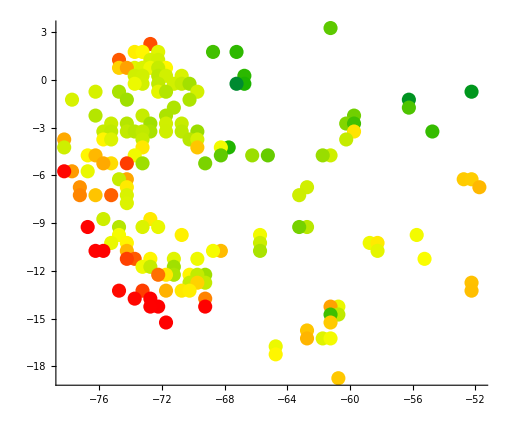

```mathematica
Graphics[{f[#3],PointSize[0.02],Point[{#1,#2}]}&@@@dataXYZ,Axes->True]
```

```mathematica
f[x_]:= Blend[{{0,Red},{10,Yellow}, {20,Darker@Green},{30,Blue}},x]
```

```mathematica
Export["AvitabilieStationAGB.tsv", dataXYZ]
```

AvitabilieStationAGB.tsv

```mathematica
basinAvitabileOverlapIndexces
```

{438,466,472,476,477,483,486,488,496,501,506,510,511,518,522,525,526,540,541,544,545,546,548,552,554,555,557,559,561,563,564,568,570,571,572,576,579,585,586,588,590,598,601,608,609,611,614,616,619,621,622,626,627,629,634,635,636,638,639,640,642,644,646,647,648,652,653,655,657,658,659,660,661,662,663,664,665,667,669,670,671,672,673,674,676,679,680,682,683,684,686,687,688,692,694,695,696,697,698,699,700,705,706,707,708,709,711,716,718,719,720,721,722,723,724,725,726,727,729,730,731,732,733,734,735,736,737,738,739,740,741,742,743,744,745,746,747,748,749,750,754,757,759,760,761,762,765,766,767,770,771,772,773,774,775,776,778,779,782,786,787,788,789,791,795,796,800,802,803,807,808,810,812,814,816}

```mathematica
posInAB
```

{1926,1884,1860,1850,1851,1853,1857,1807,1803,1808,1755,1753,1759,1756,1754,1757,1758,1703,1700,1704,1701,1706,1714,1659,1650,1651,1658,1646,1645,1648,1652,1593,1598,1585,1594,1588,1633,1526,1533,1541,1569,1515,1485,1421,1454,1430,1427,1399,1369,1378,1376,1400,1371,1374,1322,1324,1315,1312,1313,1318,1354,1344,1316,1320,1317,1288,1268,1262,1257,1258,1252,1269,1213,1217,1206,1196,1216,1173,1148,1163,1159,1142,1143,1165,1172,1088,1087,1092,1100,1090,1026,1025,1028,977,1020,976,1021,920,943,965,914,886,862,860,858,864,809,703,697,651,670,669,646,642,649,632,594,602,612,561,544,542,575,576,490,506,526,491,494,505,511,448,446,483,451,454,445,397,398,401,352,351,356,350,354,355,309,307,308,343,254,257,296,259,251,260,207,216,209,170,169,174,191,190,158,157,133,117,109,91,93,94,72,56,25}

```mathematica
basinCoords[[posInAB]]
```

{{-61.25,3.25},{-72.75,2.25},{-67.25,1.75},{-73.75,1.75},{-73.25,1.75},{-72.25,1.75},{-68.75,1.75},{-72.75,1.25},{-74.75,1.25},{-72.25,1.25},{-73.75,0.75},{-74.75,0.75},{-71.75,0.75},{-73.25,0.75},{-74.25,0.75},{-72.75,0.75},{-72.25,0.75},{-72.25,0.25},{-73.75,0.25},{-71.75,0.25},{-73.25,0.25},{-70.75,0.25},{-66.75,0.25},{-66.75,-0.25},{-71.25,-0.25},{-70.75,-0.25},{-67.25,-0.25},{-73.25,-0.25},{-73.75,-0.25},{-72.25,-0.25},{-70.25,-0.25},{-72.25,-0.75},{-69.75,-0.75},{-76.25,-0.75},{-71.75,-0.75},{-74.75,-0.75},{-52.25,-0.75},{-77.75,-1.25},{-74.25,-1.25},{-70.25,-1.25},{-56.25,-1.25},{-56.25,-1.75},{-71.25,-1.75},{-76.25,-2.25},{-59.75,-2.25},{-71.75,-2.25},{-73.25,-2.25},{-60.25,-2.75},{-75.25,-2.75},{-70.75,-2.75},{-71.75,-2.75},{-59.75,-2.75},{-74.25,-2.75},{-72.75,-2.75},{-70.75,-3.25},{-69.75,-3.25},{-74.25,-3.25},{-75.75,-3.25},{-75.25,-3.25},{-72.75,-3.25},{-54.75,-3.25},{-59.75,-3.25},{-73.75,-3.25},{-71.75,-3.25},{-73.25,-3.25},{-60.25,-3.75},{-70.25,-3.75},{-73.25,-3.75},{-75.75,-3.75},{-75.25,-3.75},{-78.25,-3.75},{-69.75,-3.75},{-69.75,-4.25},{-67.75,-4.25},{-73.25,-4.25},{-78.25,-4.25},{-68.25,-4.25},{-61.25,-4.75},{-73.75,-4.75},{-66.25,-4.75},{-68.25,-4.75},{-76.75,-4.75},{-76.25,-4.75},{-65.25,-4.75},{-61.75,-4.75},{-75.25,-5.25},{-75.75,-5.25},{-73.25,-5.25},{-69.25,-5.25},{-74.25,-5.25},{-77.75,-5.75},{-78.25,-5.75},{-76.75,-5.75},{-74.25,-6.25},{-52.75,-6.25},{-74.75,-6.25},{-52.25,-6.25},{-74.25,-6.75},{-62.75,-6.75},{-51.75,-6.75},{-77.25,-6.75},{-63.25,-7.25},{-75.25,-7.25},{-76.25,-7.25},{-77.25,-7.25},{-74.25,-7.25},{-74.25,-7.75},{-72.75,-8.75},{-75.75,-8.75},{-72.25,-9.25},{-62.75,-9.25},{-63.25,-9.25},{-74.75,-9.25},{-76.75,-9.25},{-73.25,-9.25},{-55.75,-9.75},{-74.75,-9.75},{-70.75,-9.75},{-65.75,-9.75},{-65.75,-10.25},{-74.25,-10.25},{-75.25,-10.25},{-58.75,-10.25},{-58.25,-10.25},{-76.25,-10.75},{-68.25,-10.75},{-58.25,-10.75},{-75.75,-10.75},{-74.25,-10.75},{-68.75,-10.75},{-65.75,-10.75},{-72.75,-11.25},{-73.75,-11.25},{-55.25,-11.25},{-71.25,-11.25},{-69.75,-11.25},{-74.25,-11.25},{-73.25,-11.75},{-72.75,-11.75},{-71.25,-11.75},{-71.25,-12.25},{-71.75,-12.25},{-69.25,-12.25},{-72.25,-12.25},{-70.25,-12.25},{-69.75,-12.25},{-69.25,-12.75},{-70.25,-12.75},{-69.75,-12.75},{-52.25,-12.75},{-73.25,-13.25},{-71.75,-13.25},{-52.25,-13.25},{-70.75,-13.25},{-74.75,-13.25},{-70.25,-13.25},{-73.75,-13.75},{-69.25,-13.75},{-72.75,-13.75},{-72.25,-14.25},{-72.75,-14.25},{-69.25,-14.25},{-60.75,-14.25},{-61.25,-14.25},{-60.75,-14.75},{-61.25,-14.75},{-61.25,-15.25},{-71.75,-15.25},{-62.75,-15.75},{-62.75,-16.25},{-61.75,-16.25},{-61.25,-16.25},{-64.75,-16.75},{-64.75,-17.25},{-60.75,-18.75}}

```mathematica
avitabileBasincoords
```

{{-61.25,3.25},{-72.75,2.25},{-67.25,1.75},{-73.75,1.75},{-73.25,1.75},{-72.25,1.75},{-68.75,1.75},{-72.75,1.25},{-74.75,1.25},{-72.25,1.25},{-73.75,0.75},{-74.75,0.75},{-71.75,0.75},{-73.25,0.75},{-74.25,0.75},{-72.75,0.75},{-72.25,0.75},{-72.25,0.25},{-73.75,0.25},{-71.75,0.25},{-73.25,0.25},{-70.75,0.25},{-66.75,0.25},{-66.75,-0.25},{-71.25,-0.25},{-70.75,-0.25},{-67.25,-0.25},{-73.25,-0.25},{-73.75,-0.25},{-72.25,-0.25},{-70.25,-0.25},{-72.25,-0.75},{-69.75,-0.75},{-76.25,-0.75},{-71.75,-0.75},{-74.75,-0.75},{-52.25,-0.75},{-77.75,-1.25},{-74.25,-1.25},{-70.25,-1.25},{-56.25,-1.25},{-56.25,-1.75},{-71.25,-1.75},{-76.25,-2.25},{-59.75,-2.25},{-71.75,-2.25},{-73.25,-2.25},{-60.25,-2.75},{-75.25,-2.75},{-70.75,-2.75},{-71.75,-2.75},{-59.75,-2.75},{-74.25,-2.75},{-72.75,-2.75},{-70.75,-3.25},{-69.75,-3.25},{-74.25,-3.25},{-75.75,-3.25},{-75.25,-3.25},{-72.75,-3.25},{-54.75,-3.25},{-59.75,-3.25},{-73.75,-3.25},{-71.75,-3.25},{-73.25,-3.25},{-60.25,-3.75},{-70.25,-3.75},{-73.25,-3.75},{-75.75,-3.75},{-75.25,-3.75},{-78.25,-3.75},{-69.75,-3.75},{-69.75,-4.25},{-67.75,-4.25},{-73.25,-4.25},{-78.25,-4.25},{-68.25,-4.25},{-61.25,-4.75},{-73.75,-4.75},{-66.25,-4.75},{-68.25,-4.75},{-76.75,-4.75},{-76.25,-4.75},{-65.25,-4.75},{-61.75,-4.75},{-75.25,-5.25},{-75.75,-5.25},{-73.25,-5.25},{-69.25,-5.25},{-74.25,-5.25},{-77.75,-5.75},{-78.25,-5.75},{-76.75,-5.75},{-74.25,-6.25},{-52.75,-6.25},{-74.75,-6.25},{-52.25,-6.25},{-74.25,-6.75},{-62.75,-6.75},{-51.75,-6.75},{-77.25,-6.75},{-63.25,-7.25},{-75.25,-7.25},{-76.25,-7.25},{-77.25,-7.25},{-74.25,-7.25},{-74.25,-7.75},{-72.75,-8.75},{-75.75,-8.75},{-72.25,-9.25},{-62.75,-9.25},{-63.25,-9.25},{-74.75,-9.25},{-76.75,-9.25},{-73.25,-9.25},{-55.75,-9.75},{-74.75,-9.75},{-70.75,-9.75},{-65.75,-9.75},{-65.75,-10.25},{-74.25,-10.25},{-75.25,-10.25},{-58.75,-10.25},{-58.25,-10.25},{-76.25,-10.75},{-68.25,-10.75},{-58.25,-10.75},{-75.75,-10.75},{-74.25,-10.75},{-68.75,-10.75},{-65.75,-10.75},{-72.75,-11.25},{-73.75,-11.25},{-55.25,-11.25},{-71.25,-11.25},{-69.75,-11.25},{-74.25,-11.25},{-73.25,-11.75},{-72.75,-11.75},{-71.25,-11.75},{-71.25,-12.25},{-71.75,-12.25},{-69.25,-12.25},{-72.25,-12.25},{-70.25,-12.25},{-69.75,-12.25},{-69.25,-12.75},{-70.25,-12.75},{-69.75,-12.75},{-52.25,-12.75},{-73.25,-13.25},{-71.75,-13.25},{-52.25,-13.25},{-70.75,-13.25},{-74.75,-13.25},{-70.25,-13.25},{-73.75,-13.75},{-69.25,-13.75},{-72.75,-13.75},{-72.25,-14.25},{-72.75,-14.25},{-69.25,-14.25},{-60.75,-14.25},{-61.25,-14.25},{-60.75,-14.75},{-61.25,-14.75},{-61.25,-15.25},{-71.75,-15.25},{-62.75,-15.75},{-62.75,-16.25},{-61.75,-16.25},{-61.25,-16.25},{-64.75,-16.75},{-64.75,-17.25},{-60.75,-18.75}}